```mathematica
<<Combinatorica`
```

```mathematica
rr[L_,p_]:=Delete[L,Map[List,Select[Table[If[Random[]<p,1,0],{n m}]Range[n m],#>0&]]]
```

```mathematica
ar[L_]:=L[[1]]->L[[2]]
```

```mathematica
shift[L_,vec_]:=Map[#+vec&,L]
```

```mathematica
rd[L_]:=Module[{LL,i},
LL=L;
For[i=2,i≤Length[LL],i++,
If[MemberQ[Take[LL,i-1],LL[[i]]],LL=Delete[LL,i];i=i-1]];LL]
```

```mathematica
n=9;m=6;p=.17;pp=.14;
For[y=1,y>0,y++,
ve=Union[rr[Flatten[Table[{i,j},{i,1,n},{j,1,m}],1],p],{{1,1},{n,1},{1,m},{n,m}}];
ed={};
For[i=1,i<Length[ve],i++,
If[ve[[i,1]]==ve[[i+1,1]],AppendTo[ed,{ve[[i]],ve[[i+1]]}]]];
ve=Sort[Map[Reverse,ve]];
For[i=1,i<Length[ve],i++,
If[ve[[i,1]]==ve[[i+1,1]],AppendTo[ed,{Reverse[ve[[i]]],Reverse[ve[[i+1]]]}]]];
ed=rr[ed,pp];
ve=Sort[Map[Reverse,ve]];
If[Length[ve]>.8m n,
h=HamiltonianCycle[FromUnorderedPairs[Map[Position[ve,#][[1,1]]&,ed,{2}]],All];
If[Length[h]==2,h=Map[ve[[#]]&,h[[1]]];hh=N[Partition[h,2,1]~Join~Partition[Reverse[h],2,1]];
g=GraphPlot[Map[ar,ed],VertexCoordinateRules->rd[Flatten[ed,1]],VertexRenderingFunction->({EdgeForm[Black],Hue[.1,.4],Disk[#1,0.3],Black}&),EdgeRenderingFunction->(If[#1[[1,1]]==#1[[2,1]],{White,Rectangle[#1[[1]]-{.08,0},#1[[2]]+{.08,0}],Black,Line[shift[#1,{-.08,0}]],Line[shift[#1,{.08,0}]]},{White,Rectangle[#1[[1]]-{0,.08},#1[[2]]+{0,.08}],Black,Line[shift[#1,{0,-.08}]],Line[shift[#1,{0,.08}]]}]&),ImageSize->{45(n+1),45(m+1)},PlotRange->{{0,n+1},{0,m+1}}];
Print[Style[g,Antialiasing->False]];
g1=GraphPlot[Map[ar,ed],VertexCoordinateRules->rd[Flatten[ed,1]],VertexRenderingFunction->({EdgeForm[Black],Hue[.1,.4],Disk[#1,0.3],Black}&),EdgeRenderingFunction->(If[#1[[1,1]]==#1[[2,1]],{If[MemberQ[hh,#1],Red,White],Rectangle[#1[[1]]-{.08,0},#1[[2]]+{.08,0}],Black,Line[shift[#1,{-.08,0}]],Line[shift[#1,{.08,0}]]},{If[MemberQ[hh,#1],Red,White],Rectangle[#1[[1]]-{0,.08},#1[[2]]+{0,.08}],Black,Line[shift[#1,{0,-.08}]],Line[shift[#1,{0,.08}]]}]&),ImageSize->{45(n+1),45(m+1)},PlotRange->{{0,n+1},{0,m+1}}];
Print[Style[g1,Antialiasing->False]]]]]
```

$Aborted

## 9x6 good

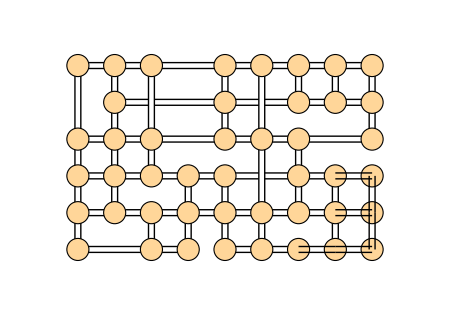

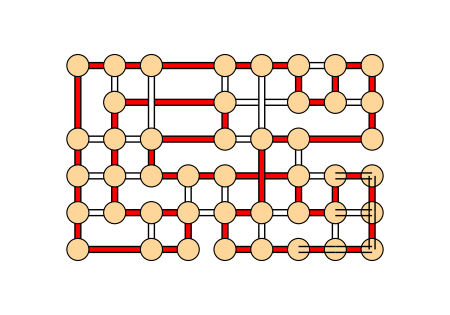

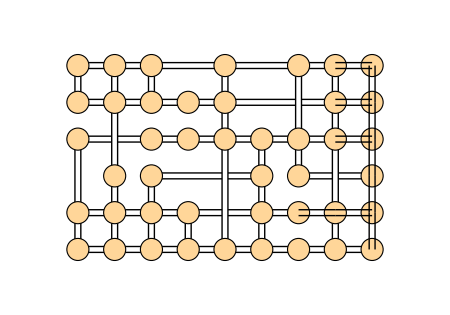

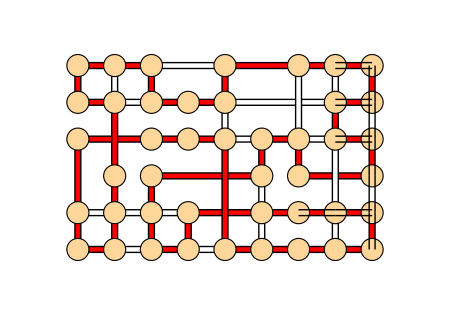

## 9x6 okay

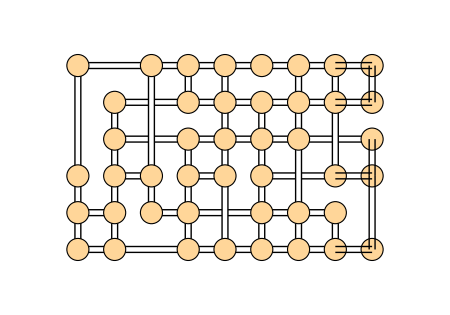

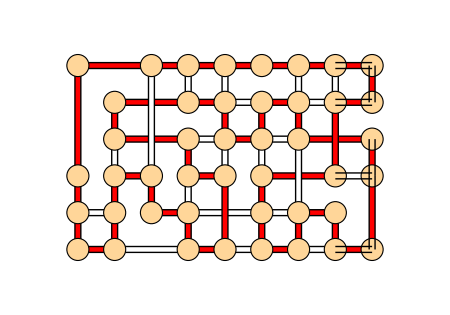

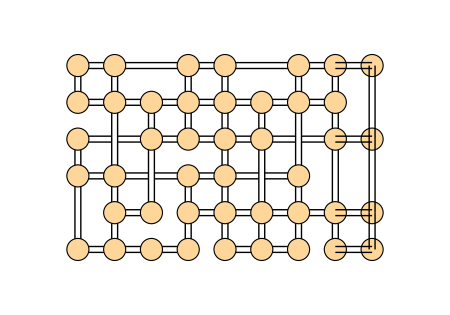

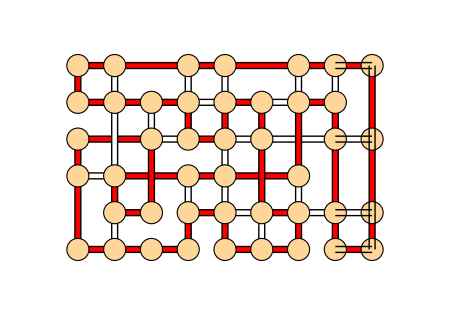

## 10x5

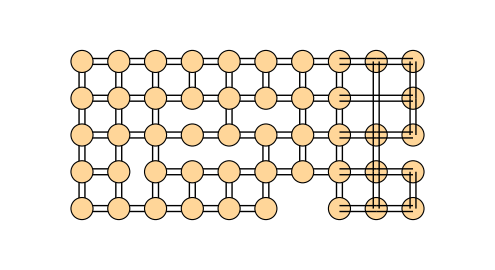

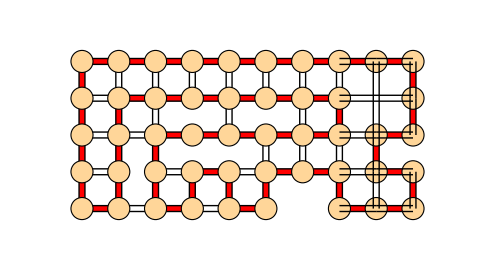

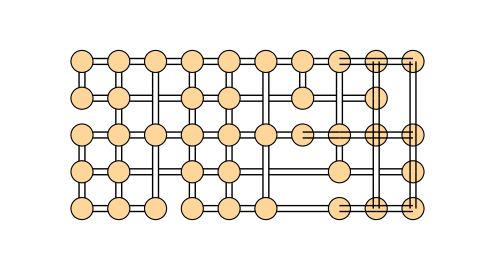

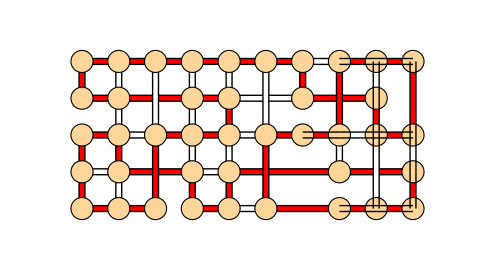

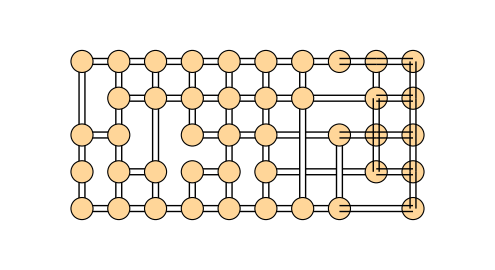

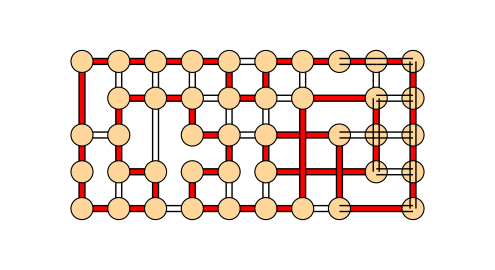

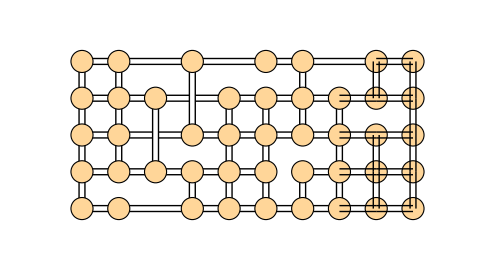

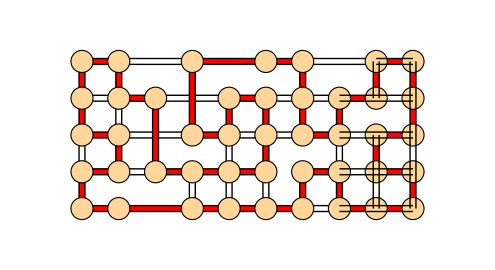

## 7x7

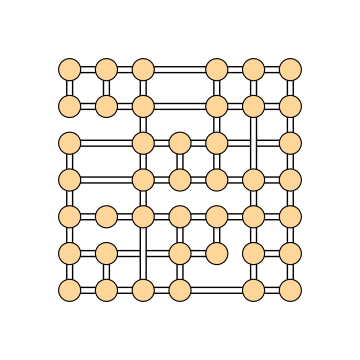

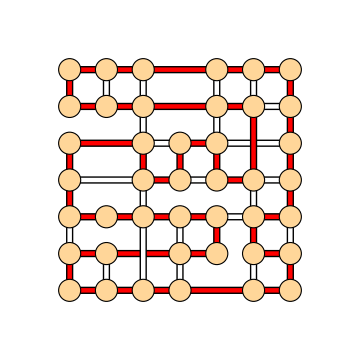

$Aborted

## 7x6